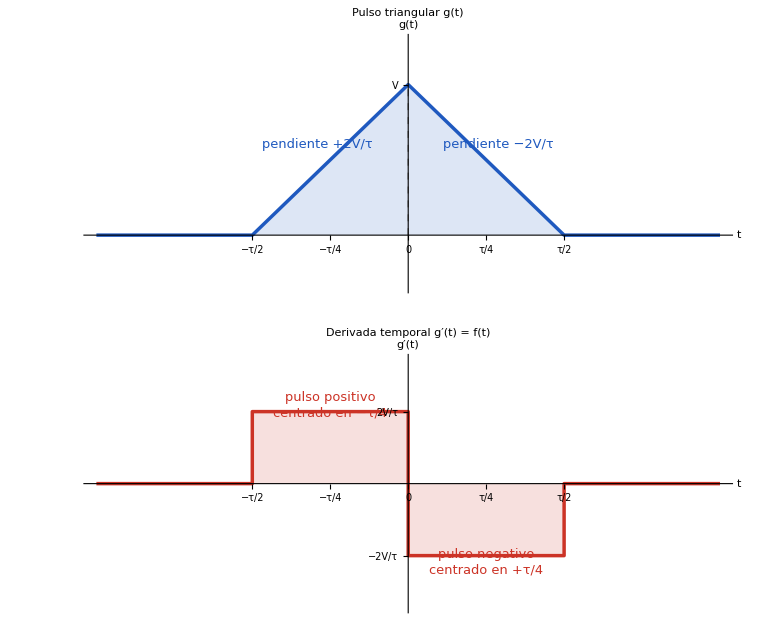

```mathematica
(* ================================================================HUECO:Pulso Triangular y su Derivada Temporal Arriba:g(t).Abajo:g'(t)=dos pulsos rectangulares de±2V/τ================================================================*)Clear[Vn,τn,An,colG,colF,estilo,xticks,figG,figF,figHueco];

Vn=2;τn=3;        (*valores ilustrativos:solo fijan la escala del dibujo*)
An=2 Vn/τn;          (*altura de los pulsos de la derivada=2V/τ*)
colG=RGBColor[0.12,0.35,0.75];
colF=RGBColor[0.80,0.20,0.15];

estilo={Axes->True,AxesOrigin->{0,0},ImageSize->1200,AspectRatio->0.42,ImagePadding->{{60,25},{28,32}},BaseStyle->{FontFamily->"Times",FontSize->14}};

xticks={{-τn/2,"−τ/2"},{-τn/4,"−τ/4"},{0,"0"},{τn/4,"τ/4"},{τn/2,"τ/2"}};

(*----Panel superior:g(t)----*)
figG=Graphics[{{colG,Opacity[0.15],Polygon[{{-τn/2,0},{0,Vn},{τn/2,0}}]},{colG,AbsoluteThickness[2.5],Line[{{-τn,0},{-τn/2,0},{0,Vn},{τn/2,0},{τn,0}}]},{GrayLevel[0.5],Dashed,Line[{{0,0},{0,Vn}}]},Text[Style["pendiente +2V/τ",colG,13],{-τn/4-0.12,Vn/2+0.2},{1,0}],Text[Style["pendiente −2V/τ",colG,13],{τn/4+0.12,Vn/2+0.2},{-1,0}]},Ticks->{xticks,{{Vn,"V"}}},AxesLabel->{"t","g(t)"},PlotRange->{{-τn,τn},{-0.35 Vn,1.3 Vn}},PlotLabel->Style["Pulso triangular g(t)",Bold,15],Sequence@@estilo];

(*----Panel inferior:g'(t)=p(t+τ/4)−p(t−τ/4)----*)
figF=Graphics[{{colF,Opacity[0.15],Polygon[{{-τn/2,0},{-τn/2,An},{0,An},{0,0}}],Polygon[{{0,0},{0,-An},{τn/2,-An},{τn/2,0}}]},{colF,AbsoluteThickness[2.5],Line[{{-τn,0},{-τn/2,0},{-τn/2,An},{0,An},{0,-An},{τn/2,-An},{τn/2,0},{τn,0}}]},Text[Style["pulso positivo\ncentrado en −τ/4",colF,13],{-τn/4,An+0.12},{0,-1}],Text[Style["pulso negativo\ncentrado en +τ/4",colF,13],{τn/4,-An-0.12},{0,1}]},Ticks->{xticks,{{An,"2V/τ"},{-An,"−2V/τ"}}},AxesLabel->{"t","g′(t)"},PlotRange->{{-τn,τn},{-2.3,2.3}},PlotLabel->Style["Derivada temporal g′(t) = f(t)",Bold,15],Sequence@@estilo];

figHueco=GraphicsColumn[{figG,figF},Spacings->0,Alignment->Center]

Export[FileNameJoin[{NotebookDirectory[],"S1S1_1_a.png"}],figHueco,ImageResolution->300];
```

```mathematica
(* ================================================================EJEMPLO 2—Serie de Fourier del tren de pulsos triangulares T=6 s,V=4 V,τ=2 s================================================================*)Clear[T0,τ0,V0,ω1,Xw,cn,tri,cnInt,c0,c1,ωBW,fBW,n,k,t,ω];

T0=6;τ0=2;V0=4;

(*----------Apartado a)----------*)
ω1=2 π/T0;                                  (*π/3 rad/s*)
Xw[ω_]:=V0 τ0/2 Sinc[ω τ0/4]^2;             (*resultado del Ejemplo 1*)
cn[n_]:=Xw[n ω1]/T0;                        (*c_n=X(nω1)/T*)

Print["ω1 = ",ω1," rad/s"];
Print["X(ω) = ",Simplify[Xw[ω]]];
Print["c_n = ",Simplify[cn[n]]];

(*Comprobación:c_n calculado directamente por integración sobre un período*)
tri[t_]:=V0 HeavisideLambda[2 t/τ0];
cnInt[k_]:=NIntegrate[tri[t] Exp[-I k ω1 t],{t,-T0/2,-τ0/2,0,τ0/2,T0/2}]/T0;
Print[TableForm[Table[{k,N[cn[k]],Chop[cnInt[k]]},{k,0,6}],TableHeadings->{None,{"n","c_n (fórmula)","c_n (integral numérica)"}}]];

(*----------Apartado b)----------*)
c0=Integrate[tri[t],{t,-T0/2,T0/2}]/T0;  (*área/T*)
c1=Simplify[cn[1]];
Print["c0 = ",c0," = ",N[c0]," V"];
Print["c1 = ",c1," = ",N[c1]," V"];

(*----------Apartado c)----------*)
ωBW=ω/. First[Solve[ω τ0/4==π,ω]];
fBW=ωBW/(2 π);
Print["ωBW = ",ωBW," rad/s     fBW = ",fBW," Hz     (armónico n = ",ωBW/ω1,")"];
Print["X(ωBW) = ",Xw[ωBW]];
Print["¿Algún cero en (0, ωBW)?  ",Reduce[Sin[ω τ0/4]==0&&0<ω<ωBW,ω]];
```

ω1 = π/3 rad/s

X(ω) = 4 Sinc[ω/2]^2

c_n = 2/3 Sinc[(n π)/6]^2

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.99999615071571260003527542668116945279166429827455431222915649414}. NIntegrate obtained -3.82696×10^-16+2.22045×10^-16 ⅈ and 3.69097×10^-16 for the integral and error estimates.

n | c_n (fórmula) | c_n (integral numérica)
0 | 0.666667 | 0.666667
1 | 0.607927 | 0.607927
2 | 0.455945 | 0.455945
3 | 0.27019 | 0.27019
4 | 0.113986 | 0.113986
5 | 0.0243171 | 0.0243171
6 | 0. | 0

c0 = 2/3 = 0.666667 V

c1 = 6/π^2 = 0.607927 V

ωBW = 2 π rad/s     fBW = 1 Hz     (armónico n = 6)

X(ωBW) = 0

¿Algún cero en (0, ωBW)?  False

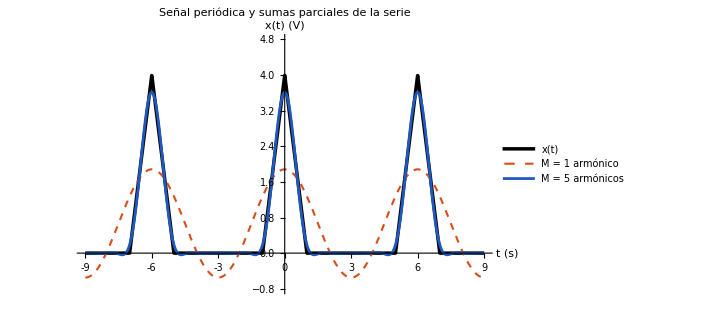

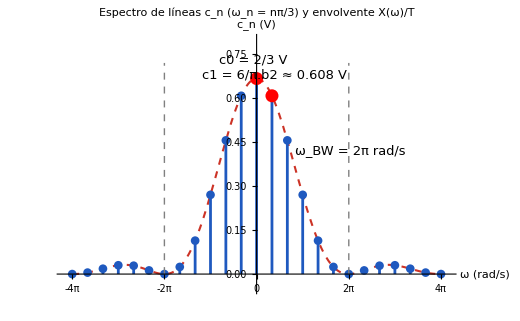

```mathematica
Clear[xper,serie,figSenal,figEsp,nmax,puntosEsp];

(*----------Señal periódica y sumas parciales de la serie----------*)
xper[t_]:=V0 HeavisideLambda[2 Mod[t,T0,-T0/2]/τ0];
serie[t_,M_]:=cn[0]+2 Sum[cn[k] Cos[k ω1 t],{k,1,M}];

figSenal=Plot[{xper[t],serie[t,1],serie[t,5]},{t,-9,9},PlotStyle->{{AbsoluteThickness[2.5],Black},{AbsoluteThickness[1.5],Dashed,RGBColor[0.85,0.30,0.10]},{AbsoluteThickness[2],RGBColor[0.12,0.35,0.75]}},Exclusions->None,PlotRange->{-0.8,4.8},Ticks->{Range[-9,9,3],Automatic},AxesLabel->{"t (s)","x(t) (V)"},PlotLabel->Style["Señal periódica y sumas parciales de la serie",Bold,14],PlotLegends->Placed[LineLegend[{"x(t)","M = 1 armónico","M = 5 armónicos"}],Below],ImageSize->520,BaseStyle->{FontFamily->"Times",FontSize->13}]

(*----------Espectro de líneas c_n sobre la envolvente X(ω)/T----------*)
nmax=12;
puntosEsp=Table[{k ω1,cn[k]},{k,-nmax,nmax}];

figEsp=Show[Plot[Xw[ω]/T0,{ω,-nmax ω1,nmax ω1},PlotStyle->{AbsoluteThickness[1.5],Dashed,RGBColor[0.80,0.20,0.15]}],ListPlot[puntosEsp,Filling->Axis,PlotStyle->{PointSize[0.012],RGBColor[0.12,0.35,0.75]},FillingStyle->Directive[AbsoluteThickness[2],RGBColor[0.12,0.35,0.75]]],Graphics[{{GrayLevel[0.5],Dashed,Line[{{ωBW,0},{ωBW,0.72}}],Line[{{-ωBW,0},{-ωBW,0.72}}]},Text[Style[Row[{Subscript["ω","BW"]," = 2π rad/s"}],13],{ωBW+0.1,0.42},{-1,0}],Text[Style["c0 = 2/3 V",13],{-0.25,0.73},{1,0}],Text[Style["c1 = 6/π.b2 ≈ 0.608 V",13],{ω1+0.2,c1+0.07},{-1,0}],{Red,PointSize[0.018],Point[{0,c0}],Point[{ω1,c1}]}}],PlotRange->{{-nmax ω1-0.5,nmax ω1+0.5},{-0.05,0.8}},Ticks->{Table[{k π,If[k==0,"0",ToString[k]<>"π"]},{k,-4,4,2}],Automatic},AxesLabel->{"ω (rad/s)","c_n (V)"},PlotLabel->Style["Espectro de líneas c_n (ω_n = nπ/3) y envolvente X(ω)/T",Bold,14],ImageSize->520,BaseStyle->{FontFamily->"Times",FontSize->13}]
```